```mathematica
PendulumCoeff={{1,0,0,0},{0,-2,0,-1},{0,1,1,0}}//DisplayForm
```

```mathematica
{{1,0,0,0},{0,-2,0,-1},{0,1,1,0}}//MatrixForm
```

```mathematica
({{1, 1, 0, 0}, {0, -2, 0, -1}, {0, 0, 1, 0}})//RowReduce//MatrixForm
```

(1 | 0 | 0 | -1/2
0 | 1 | 0 | 1/2
0 | 0 | 1 | 0)

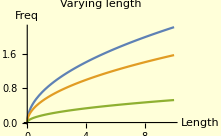

```mathematica
Plot[{{Sqrt[x]/Sqrt[2],
{{Sqrt[x/4]},
{Sqrt[x/36]}}}},
	{x,0,10}, 
PlotLabel->"Varying length",
AxesLabel->{Length,Freq},
PlotLegends->"Expressions",
Background->LightYellow]
```

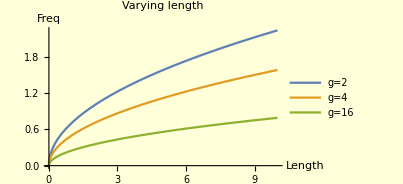

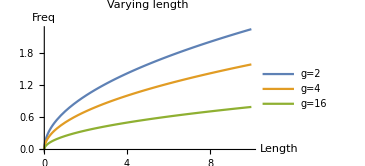

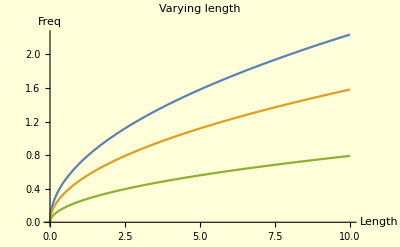

-Graphics-

```mathematica
Show[%28,Background->LightYellow]
```

```mathematica
Show[%37,PlotLegends->Automatic]
```

-Graphics-

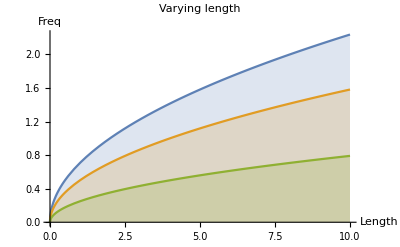

```mathematica
Plot[{{(√x)/(√2),{{√(x/4)},{√(x/16)}}}},{x,0,10},Filling->Automatic,PlotLabel->"Varying length",AxesLabel->{Length,Freq}]
```

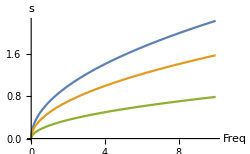

```mathematica
Show[%22,PlotLabel->None,LabelStyle->{FontFamily->"Academy Engraved LET",GrayLevel[0]}]
```

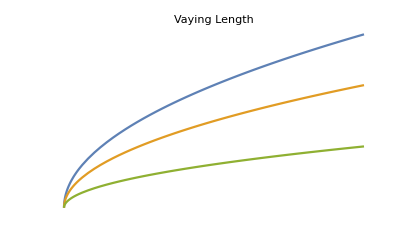

```mathematica
Show[%22,Axes->False]
```

```mathematica
Solve[2x^4==x,x]
```

{{x→0},{x→-(-1/2)^(1/3)},{x→1/2^(1/3)},{x→(-1)^(2/3)/2^(1/3)}}

```mathematica
A*Cos[2*Pi/L*x-W*t]//Simplify
```

A Cos[t W-(2 π x)/L]

```mathematica
Manipulate[Plot3D[A Cos[t W-(2 π x)/L],{t,-2 π,2 π},{x,-1,1}],{A,-2,2},{L,-2,2},{W,-2,2}]
```

```mathematica
Integrate[(Exp[I*k*x]*Exp[I*w*t])^2,{x,-Infinity,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(2 ⅈ (t w+k x)) does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(2 ⅈ t w+2 ⅈ k x)ⅆx

```mathematica
(ⅈ ⅇ^(2 ⅈ t w) (ⅇ^(2 ⅈ a k)-ⅇ^(2 ⅈ b k)))/(2 k)
```

(ⅈ ⅇ^(2 ⅈ t w) (ⅇ^(-2 ⅈ b k)-ⅇ^(2 ⅈ b k)))/(2 k)

```mathematica
Simplify[(ⅈ ⅇ^(2 ⅈ t w) (ⅇ^(-2 ⅈ b k)-ⅇ^(2 ⅈ b k)))/(2 k)]
```

-(ⅈ ⅇ^(-2 ⅈ b k+2 ⅈ t w) (-1+ⅇ^(4 ⅈ b k)))/(2 k)

```mathematica
a=-b
```

-b

```mathematica
(A^2 (4 (-a+b) π-L Sin[(4 a π)/L-2 t W]+L Sin[(4 b π)/L-2 t W]))/(8 π)//Simplify
```

(A^2 (4 (-a+b) π-L Sin[(4 a π)/L-2 t W]+L Sin[(4 b π)/L-2 t W]))/(8 π)

```mathematica
Manipulate[Plot[(A^2 (4 (-a+b) π-L Sin[(4 a π)/L-2 t W]+L Sin[(4 b π)/L-2 t W]))/(8 π),{t,-3.141592653589793,3.141592653589793}],{a,-0.3408450569081046,0.6591549430918953},{A,-2,2},{b,-2,2},{L,-2,2},{W,-2,2}]
```

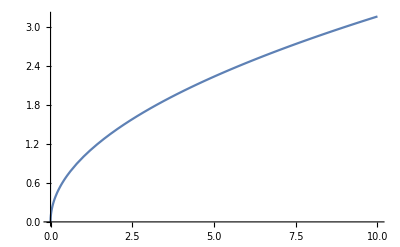

```mathematica
Plot[Sqrt[x],{x,0,10}]
```

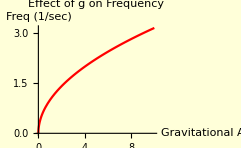

```mathematica
Plot[{Sqrt[x]},
	{x,0,10}, PlotStyle->Red,
PlotLabel->"Effect of g on Frequency",
AxesLabel->{"Gravitational
Acceleration 
(units of g)","Freq 
(1/sec)"},
PlotLegends->"Expressions",
Background->LightYellow]
```

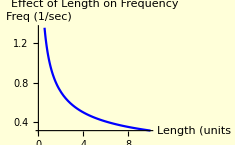

```mathematica
Plot[{Sqrt[1/x]},
	{x,0,10}, PlotStyle->Blue,
PlotLabel->"Effect of Length on Frequency",
AxesLabel->{"Length 
(units of l)","Freq 
(1/sec)"},
PlotLegends->"Expressions",
Background->LightYellow]
```

```mathematica
Limit[1/Sqrt[x],x->0]
```

Indeterminate

```mathematica
Information[Indeterminate]
```

```mathematica
({{0, 1, 0, 1}, {1, -3, 0, 2}, {0, 0, 1, -2}})//RowReduce//MatrixForm
```

(1 | 0 | 0 | 5
0 | 1 | 0 | 1
0 | 0 | 1 | -2)

```mathematica
18.3-13.9
```

```mathematica
4.4/18.3
```

0.240437

```mathematica
{{a,b,c},{a,b,c},{a,b,c},{a,b,c}}
```

```mathematica
{{a,b,c},{a,b,c},{a,b,c}}//MatrixForm
```

```mathematica
ClearAll[x]
```

```mathematica
({{Dt[x,p], Dt[x,ψ], Dt[x,θ]}, {a, b, c}, {a, b, c}})//MatrixForm
```

```mathematica
({{Dt[x,p], Dt[x,ψ], Dt[x,θ]}, {Dt[y,p], Dt[y,ψ], Dt[y,θ]}, {Dt[z,p], Dt[z,ψ], Dt[z,θ]}})//MatrixForm
```

(Dt[x,p] | Dt[x,ψ] | Dt[x,θ]
Dt[y,p] | Dt[y,ψ] | Dt[y,θ]
Dt[z,p] | Dt[z,ψ] | Dt[z,θ])